## Imports and helper functions

Note: for this notebook to function properly the following package are required: QM, QuantumWalks, MaTeX.

```mathematica
Needs["QM`"];
Needs["QuantumWalks`"];
Needs["utilities`"];

Needs["GeneralUtilities`"];
Needs["MaTeX`"];
```

```mathematica
normalizePhase[expr_?MatrixQ]:=expr Exp[-I Arg@expr⟦1,1⟧]//Chop;
normalizePhase[expr_List]:=expr Exp[-I Arg@expr⟦1⟧]//Chop;
```

```mathematica
ClearAll@monitorMap;
Attributes@monitorMap=HoldAll;
monitorMap[Map[func_,target_]]:=Module[{iter=0},
Monitor[
Map[(iter++;func@#)&,target],
progressBar[100.iter/Length@target]
]
];
```

## Visualization of simple discrete-time, one-dimensional quantum walk evolutions with fixed coins

State of a walker after 2 steps, with fixed Hadamard coin, with coin start in up position:

```mathematica
state=QWEvolve[{1,0},HadamardMatrix[2],1]//QState//QStateChangeBasis@{{1,2},{"↑","↓"}}
```

-Graphics-

Many steps of Hadamard evolution, with up and down initial coin states:

```mathematica
hadamardEvolution[initialCoinState_,nSteps_]:=QWEvolve[
initialCoinState,ConstantArray[N@HadamardMatrix@2,nSteps]
]//Partition[#,2]&//Transpose;
```

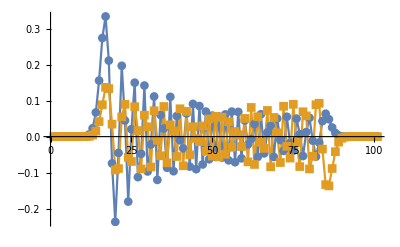
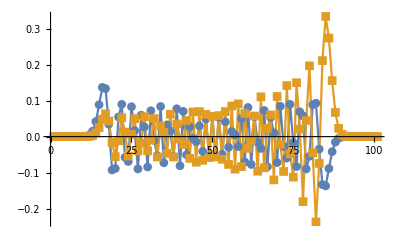

```mathematica
ListPlot[
hadamardEvolution[#,100],
PlotRange->All,ImageSize->400,
Joined->True,PlotMarkers->Automatic
]&/@{{1,0},{0,1}}
```

Many steps of Hadamard evolution, with different balanced inital coin states ({1, 1} and {1, I}):

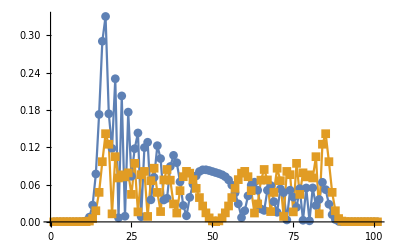
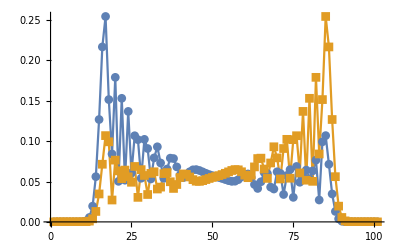

```mathematica
ListPlot[
Abs@hadamardEvolution[#,100],
PlotRange->All,ImageSize->400,
Joined->True,PlotMarkers->Automatic
]&/@Normalize/@{{1,1},{1,I}}
```

```mathematica
QWEvolve[{1,0},HadamardMatrix[2],2]
```

{Cos[1/(√2)]^2,0,-Sin[1/(√2)]^2,-ⅇ^(ⅈ/(√2)) Cos[1/(√2)] Sin[1/(√2)],0,-ⅇ^(ⅈ/(√2)) Cos[1/(√2)] Sin[1/(√2)]}

```mathematica
QWEvolve[{1,0},HadamardMatrix[2]]
```

{Cos[1/(√2)]^2,0,-Sin[1/(√2)]^2,-ⅇ^(ⅈ/(√2)) Cos[1/(√2)] Sin[1/(√2)],0,-ⅇ^(ⅈ/(√2)) Cos[1/(√2)] Sin[1/(√2)]}

Many steps with same coin operation, parametrized by θ. We here look at the amplitudes associated with ↑ and ↓ coin states (blue and orange, respectively) obtained after 30 steps, for the various possible values of θ.

```mathematica
DynamicModule[{nSteps,outAmps},
nSteps=30;
outAmps[θ_]:=QWEvolve[{1,0},ConstantArray[{θ},nSteps]]//Partition[#,2]&//Transpose;
Manipulate[
ListPlot[outAmps[θ],
PlotRange->{All,{-1,1}},Joined->True,PlotMarkers->Automatic
],
{{θ,Pi/2},0,Pi,0.01,Appearance->"Labeled"}
]
]
```